```mathematica
greenRoutes = {
{"El Paso","Houston",6, Green},
{"Portland","San Francisco",5, Green},
{"Saint Louis","Pittsburgh", 5, Green},
{"Helena","Denver",4, Green},
{"Little Rock","New Orleans", 3, Green},
{"Chicago","Saint Louis",2, Green},
{"Pittsburgh", "New York",2, Green}
};
pinkRoutes = {
{"Duluth","Toronto",6, Pink},
{"Portland","San Francisco",5, Pink},
{"Denver","Omaha",4, Pink},
{"Charleston","Miami",4, Pink},
{"San Francisco","Los Angeles",3, Pink},
{"Helena","Salt Lake City",3, Pink},
{"Kansas City","Saint Louis",2, Pink}
};
blackRoutes = {
{"Los Angeles", "El Paso",6, Black},
{"Sault St. Marie","Montreal",5, Black},
{"Denver","Kansas City",4, Black},
{"Winnipeg","Duluth",4, Black},
{"Nashville","Raleigh",3, Black},
{"Chicago","Pittsburgh",3, Black},
{"New York","Washington",2, Black}
};
orangeRoutes = {
{"Helena","Duluth",6, Orange},
{"San Francisco","Salt Lake City",5, Orange},
{"Denver", "Kansas City",4, Orange},
{"New Orleans","Atlanta",4, Orange},
{"Las Vegas","Salt Lake City",3, Orange},
{"Chicago","Pittsburgh",3, Orange},
{"New York","Washington",2, Orange}
};
yellowRoutes = {
{"Seattle","Helena",6, Yellow},
{"El Paso","Oklahoma City",5, Yellow},
{"New Orleans","Atlanta",4, Yellow},
{"Nashville","Pittsburgh",4, Yellow},
{"San Francisco","Los Angeles",3, Yellow},
{"Salt Lake City","Denver",3, Yellow},
{"Boston","New York",2, Yellow}
};
blueRoutes = {
{"Portland","Salt Lake City", 6, Blue},
{"Atlanta","Miami",5, Blue},
{"Helena","Winnipeg",4, Blue},
{"Omaha", "Chicago",4, Blue},
{"Santa Fe","Oklahoma City",3, Blue},
{"Montreal","New York",3, Blue},
{"Kansas City","Saint Louis",2, Blue}
};
redRoutes = {
{"New Orleans","Miami",6, Red},
{"Helena","Omaha",5, Red},
{"El Paso","Dallas",4, Red},
{"Denver","Oklahoma City",4, Red},
{"Salt Lake City","Denver",3, Red},
{"Duluth","Chicago",3, Red},
{"Boston","New York",2, Red}
};
whiteRoutes = {
{"Calgary","Winnipeg",6, Dashed},
{"San Francisco","Salt Lake City",5, Dashed},
{"Phoenix","Denver",5, Dashed},
{"Chicago","Toronto",4, Dashed},
{"Little Rock","Nashville",3, Dashed},
{"Chicago","Saint Louis",2, Dashed},
{"Pittsburgh", "New York",2, Dashed}
};
greyRoutes={
{"Winnipeg","Sault St. Marie",6,Gray},
{"Seattle","Calgary",4,Gray},
{"Calgary","Helena",4,Gray},
{"Vancouver","Calgary",3,Gray},
{"Los Angeles","Phoenix",3,Gray},
{"Sault St. Marie","Duluth",3,Gray},
{"Phoenix", "Santa Fe",3,Gray},
{"Phoenix","El Paso",3,Gray},
{"Toronto","Montreal",3,Gray},
{"Montreal","Boston",2,Gray},
{"Montreal","Boston",2,Gray},
{"Houston","New Orleans",2,Gray},
{"Dallas","Little Rock",2,Gray},
{"Oklahoma City","Little Rock",2,Gray},
{"Santa Fe","El Paso",2,Gray},
{"Los Angeles","Las Vegas",2,Gray},
{"Duluth","Omaha",2,Gray},
{"Duluth","Omaha",2,Gray},
{"Duluth","Sault St. Marie",2,Gray},
{"Kansas City","Oklahoma City",2,Gray},
{"Kansas City","Oklahoma City",2,Gray},
{"Oklahoma City","Dallas",2,Gray},
{"Oklahoma City","Dallas",2,Gray},
{"Little Rock","Saint Louis",2,Gray},
{"Saint Louis","Nashville",2,Gray},
{"Atlanta", "Charleston",2,Gray},
{"Atlanta","Raleigh",2,Gray},
{"Atlanta","Raleigh",2,Gray},
{"Raleigh", "Charleston",2,Gray},
{"Raleigh","Washington",2,Gray},
{"Raleigh","Washington",2,Gray},
{"Raleigh","Pittsburgh",2,Gray},
{"Pittsburgh","Washington",2,Gray},
{"Sault St. Marie","Toronto",2,Gray},
{"Pittsburgh","Toronto",2,Gray},
{"Nashville","Atlanta",1,Gray},
{"Dallas","Houston",1,Gray},
{"Dallas","Houston",1,Gray},
{"Omaha","Kansas City",1,Gray},
{"Omaha","Kansas City",1,Gray},
{"Seattle","Portland",1,Gray},
{"Seattle","Portland",1,Gray},
{"Vancouver","Seattle",1,Gray},
{"Vancouver","Seattle",1,Gray}
};
```

Notes:
Green&White have a strange number of routes. 
Only one blue route doubles up.

```mathematica
edges = UndirectedEdge@@@greenRoutes[[All,1;;2]]
MapThread[Style,{edges, greenRoutes[[All,4]]}]
```

{El Paso<->Houston,Portland<->San Francisco,Saint Louis<->Pittsburgh,Helena<->Denver,Little Rock<->New Orleans,Chicago<->Saint Louis,Pittsburgh<->New York}

{El Paso<->Houston,Portland<->San Francisco,Saint Louis<->Pittsburgh,Helena<->Denver,Little Rock<->New Orleans,Chicago<->Saint Louis,Pittsburgh<->New York}

```mathematica
constructGraph[data_]:=EdgeTaggedGraph[
MapThread[Style,{UndirectedEdge@@@data[[All,1;;2]],data[[All,4]]}],
EdgeWeight->data[[All,3]],
VertexLabels->"Name",
EdgeLabels->"EdgeWeight"
]
```

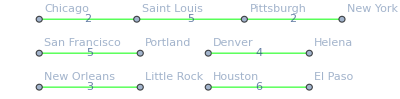

```mathematica
greenGraph = constructGraph[greenRoutes]
pinkGraph = constructGraph[pinkRoutes];
blackGraph= constructGraph[blackRoutes];
orangeGraph = constructGraph[orangeRoutes];
yellowGraph = constructGraph[yellowRoutes];
blueGraph = constructGraph[blueRoutes];
redGraph = constructGraph[redRoutes];
whiteGraph = constructGraph[whiteRoutes ];
greyGraph = constructGraph[greyRoutes];
```

```mathematica
masterGraph = constructGraph[
Join[
greenRoutes,pinkRoutes,blackRoutes,orangeRoutes,
yellowRoutes,blueRoutes,redRoutes,whiteRoutes,greyRoutes
]
]
```

{Vancouver,Seattle,Helena,Omaha,Kansas City,Saint Louis,Nashville,Atlanta,Miami}

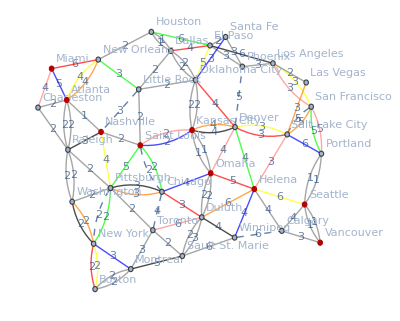

```mathematica
FindShortestPath[masterGraph,"Vancouver","Miami"]
```

```mathematica
subset = Join[pinkRoutes, greenRoutes]
```

```mathematica
{{"Duluth","Toronto",6,RGBColor[1, 0.5, 0.5]},{"Portland","San Francisco",5,RGBColor[1, 0.5, 0.5]},{"Denver","Omaha",4,RGBColor[1, 0.5, 0.5]},{"Charleston","Miami",4,RGBColor[1, 0.5, 0.5]},{"San Francisco","Los Angeles",3,RGBColor[1, 0.5, 0.5]},{"Helena","Salt Lake City",3,RGBColor[1, 0.5, 0.5]},{"Kansas City","Saint Louis",2,RGBColor[1, 0.5, 0.5]},{"El Paso","Houston",6,RGBColor[0, 1, 0]},{"Portland","San Francisco",5,RGBColor[0, 1, 0]},{"Saint Louis","Pittsburgh",5,RGBColor[0, 1, 0]},{"Helena","Denver",4,RGBColor[0, 1, 0]},{"Little Rock","New Orleans",3,RGBColor[0, 1, 0]},{"Chicago","Saint Louis",2,RGBColor[0, 1, 0]},{"Pittsburgh","New York",2,RGBColor[0, 1, 0]}}
EdgeTaggedGraph[MapThread[Style,{UndirectedEdge@@@subset[[All,1;;2]],subset[[All,4]]}]]
```

{{Duluth,Toronto,6,RGBColor[1, 0.5, 0.5]},{Portland,San Francisco,5,RGBColor[1, 0.5, 0.5]},{Denver,Omaha,4,RGBColor[1, 0.5, 0.5]},{Charleston,Miami,4,RGBColor[1, 0.5, 0.5]},{San Francisco,Los Angeles,3,RGBColor[1, 0.5, 0.5]},{Helena,Salt Lake City,3,RGBColor[1, 0.5, 0.5]},{Kansas City,Saint Louis,2,RGBColor[1, 0.5, 0.5]},{El Paso,Houston,6,RGBColor[0, 1, 0]},{Portland,San Francisco,5,RGBColor[0, 1, 0]},{Saint Louis,Pittsburgh,5,RGBColor[0, 1, 0]},{Helena,Denver,4,RGBColor[0, 1, 0]},{Little Rock,New Orleans,3,RGBColor[0, 1, 0]},{Chicago,Saint Louis,2,RGBColor[0, 1, 0]},{Pittsburgh,New York,2,RGBColor[0, 1, 0]}}

-Graphics-

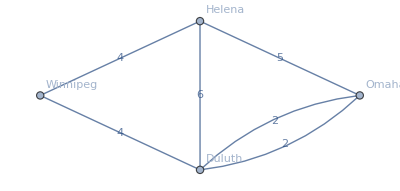

```mathematica
test = Graph[
{
"Helena"<->"Duluth",
"Helena"<->"Winnipeg",
"Winnipeg"<->"Duluth",
"Helena"<->"Omaha",
"Omaha"<->"Duluth",
"Omaha"<->"Duluth"
},
EdgeWeight->{6,4,4,5,2,2},
VertexLabels->"Name",
EdgeLabels->"EdgeWeight"]
```

```mathematica
FindShortestPath[test, "Winnipeg","Omaha"]
```

{Winnipeg,Duluth,Omaha}

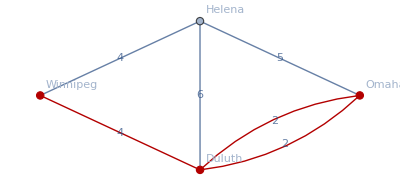

```mathematica
HighlightGraph[Graph[{"Helena", "Duluth", "Winnipeg", "Omaha"}, {UndirectedEdge["Helena", "Duluth"], UndirectedEdge["Helena", "Winnipeg"], UndirectedEdge["Winnipeg", "Duluth"], UndirectedEdge["Helena", "Omaha"], UndirectedEdge["Omaha", "Duluth"], UndirectedEdge["Omaha", "Duluth"]}, {EdgeLabels -> {"EdgeWeight"}, VertexLabels -> {"Name"}, EdgeWeight -> {6, 4, 4, 5, 2, 2}}],PathGraph[{"Winnipeg","Duluth","Omaha"}]]
```

```mathematica
AdjacencyMatrix[test]
```

SparseArray[…]

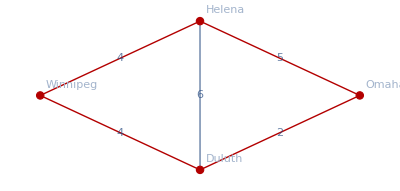

```mathematica
HighlightGraph[test,PathGraph[{"Helena", "Duluth", "Winnipeg", "Omaha"}[[%21[[2]]]]]]
```

```mathematica
test
```

-Graphics-

```mathematica
DeleteDuplicates[test, Sort]
```

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[,Sort].

DeleteDuplicates[-Graphics-,Sort]

```mathematica
WeightedAdjacencyMatrix[test]
```

SparseArray[…]

```mathematica
Grid[%38]
```

0 | 6 | 4 | 5
6 | 0 | 4 | 4
4 | 4 | 0 | 0
5 | 4 | 0 | 0

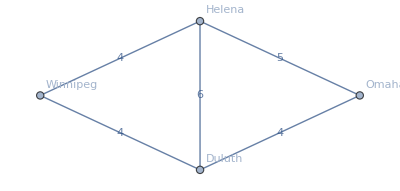

```mathematica
SimpleGraph[test]
```

```mathematica
EdgeList[test]
```

{Helena<->Duluth,Helena<->Winnipeg,Winnipeg<->Duluth,Helena<->Omaha,Omaha<->Duluth,Omaha<->Duluth}

```mathematica
PropertyValue[test, EdgeWeight]
```

{6,4,4,5,2,2}

```mathematica
Thread[{EdgeList[test], PropertyValue[test, EdgeWeight]}]
```

{{Helena<->Duluth,6},{Helena<->Winnipeg,4},{Winnipeg<->Duluth,4},{Helena<->Omaha,5},{Omaha<->Duluth,2},{Omaha<->Duluth,2}}

```mathematica
DeleteDuplicates[%]
```

{{Helena<->Duluth,6},{Helena<->Winnipeg,4},{Winnipeg<->Duluth,4},{Helena<->Omaha,5},{Omaha<->Duluth,2}}

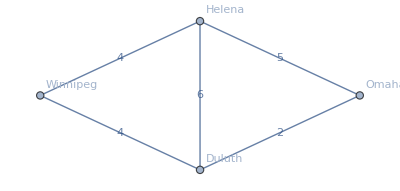

```mathematica
Graph[%48[[All,1]],EdgeWeight->%48[[All,2]],VertexLabels->"Name",
EdgeLabels->"EdgeWeight"]
```